```mathematica
(*Definition of Clausen.*)Cl2[θ_]/;NumberQ[θ]:=Sum[Sin[k θ]/k^2,{k,1,1500}]//N
Derivative[1][Cl2][θ_]=-Log[2 Sin[θ/2]];

(*This series converges more fast.*)

Cl2[θ_]/;NumberQ[θ]:=θ (3-Log[Abs[θ] (1-θ^2/(4 Pi^2))])-2 Pi Log[(2 Pi+θ)/(2 Pi-θ)]+θ Sum[(Zeta[2 k]-1)/(k (2 k+1)) (θ/(2 Pi))^(2 k),{k,1,2}]//N

K[e_]/;NumberQ[e]:=Cl2[2 ArcCos[-(1/e)]]+ArcCos[-(1/e)] Log[-(2/e)+2 e]
(*-------------------------------------------------------------------------------------------------------------------------------------------------------*)
MS:=2 10^30

rel:={η->0.2,ξ->1/105,c->3 10^8,G->6.674 10^-11,Ω->0.5,et->4}
rel3:={η->0.2,ξ->1/50,c->3 10^8,G->6.674 10^-11,Ω->0.5,et->4}
(*-------------------------------------------------------------------------------------------------------------------------------------------------------*)
y=1/c^2;(*ξ=(G M)/(b c^2);*)
scale:=MS (3 10^8)^2 10^-3
fac:=1/(15 y)(2 M η^2 ξ^(7/2) MS)/scale
Efluxb:=(602/(3 (-1+et^2)^(5/4))+(673 et^2)/(3 (-1+et^2)^(5/4))+(96/((-1+et^2)^(7/4))+(292 et^2)/((-1+et^2)^(7/4))+(37 et^4)/((-1+et^2)^(7/4))) ArcCos[-1/et]+ξ (312299/(210 (-1+et^2)^(7/4))+(620311 et^2)/(105 (-1+et^2)^(7/4))+(1772621 et^4)/(840 (-1+et^2)^(7/4))-(11389 η)/(18 (-1+et^2)^(7/4))-(159143 et^2 η)/(36 (-1+et^2)^(7/4))-(80159 et^4 η)/(36 (-1+et^2)^(7/4))+(4226/(7 (-1+et^2)^(9/4))+(33267 et^2)/(7 (-1+et^2)^(9/4))+(15611 et^4)/(4 (-1+et^2)^(9/4))+(13789 et^6)/(56 (-1+et^2)^(9/4))-(224 η)/((-1+et^2)^(9/4))-(9313 et^2 η)/(3 (-1+et^2)^(9/4))-(14635 et^4 η)/(4 (-1+et^2)^(9/4))-(3515 et^6 η)/(12 (-1+et^2)^(9/4))) ArcCos[-1/et])+ξ^2 (1201481929/(79380 (-1+et^2)^(9/4))+(1613398981 et^2)/(31752 (-1+et^2)^(9/4))+(20298633697 et^4)/(317520 (-1+et^2)^(9/4))+(574213217 et^6)/(23520 (-1+et^2)^(9/4))-(382081 η)/(60 (-1+et^2)^(9/4))-(351308243 et^2 η)/(5040 (-1+et^2)^(9/4))-(1245473359 et^4 η)/(10080 (-1+et^2)^(9/4))-(392203747 et^6 η)/(10080 (-1+et^2)^(9/4))+(12987 η^2)/(16 (-1+et^2)^(9/4))+(5330611 et^2 η^2)/(288 (-1+et^2)^(9/4))+(1749437 et^4 η^2)/(36 (-1+et^2)^(9/4))+(4957207 et^6 η^2)/(288 (-1+et^2)^(9/4))+(1250318/(189 (-1+et^2)^(11/4))+(15342815 et^2)/(378 (-1+et^2)^(11/4))+(31089259 et^4)/(504 (-1+et^2)^(11/4))+(1773305 et^6)/(42 (-1+et^2)^(11/4))+(305219 et^8)/(96 (-1+et^2)^(11/4))-(100267 η)/(42 (-1+et^2)^(11/4))-(287208 et^2 η)/(7 (-1+et^2)^(11/4))-(2483015 et^4 η)/(21 (-1+et^2)^(11/4))-(6910235 et^6 η)/(96 (-1+et^2)^(11/4))-(470645 et^8 η)/(96 (-1+et^2)^(11/4))+(237 η^2)/((-1+et^2)^(11/4))+(76797 et^2 η^2)/(8 (-1+et^2)^(11/4))+(4018115 et^4 η^2)/(96 (-1+et^2)^(11/4))+(501497 et^6 η^2)/(16 (-1+et^2)^(11/4))+(200947 et^8 η^2)/(96 (-1+et^2)^(11/4))) ArcCos[-1/et])+ξ^3 (18196134199/(107800 (-1+et^2)^(11/4))+(7267628063669 et^2)/(8731800 (-1+et^2)^(11/4))+(114384080392889 et^4)/(139708800 (-1+et^2)^(11/4))+(108093992952173 et^6)/(139708800 (-1+et^2)^(11/4))+(3415579359349 et^8)/(12418560 (-1+et^2)^(11/4))-(384062668039 η)/(1905120 (-1+et^2)^(11/4))-(177784967603 et^2 η)/(158760 (-1+et^2)^(11/4))-(4727520813649 et^4 η)/(2540160 (-1+et^2)^(11/4))-(14846272253753 et^6 η)/(7620480 (-1+et^2)^(11/4))-(307340897 et^8 η)/(504 (-1+et^2)^(11/4))+(26288831 π^2 η)/(6720 (-1+et^2)^(11/4))+(120731347 et^2 π^2 η)/(13440 (-1+et^2)^(11/4))+(90733 et^4 π^2 η)/(56 (-1+et^2)^(11/4))-(12303239 et^6 π^2 η)/(13440 (-1+et^2)^(11/4))+(5188635255233714639 η^2)/(382994320040640 (-1+et^2)^(11/4))+(2016946731240853063 et^2 η^2)/(76598864008128 (-1+et^2)^(11/4))+(358628492987748209729 et^4 η^2)/(510659093387520 (-1+et^2)^(11/4))+(1038922883478235095371 et^6 η^2)/(765988640081280 (-1+et^2)^(11/4))+(3232008020860103 et^8 η^2)/(7377156864 (-1+et^2)^(11/4))-(1460525 η^3)/(1728 (-1+et^2)^(11/4))-(130132835 et^2 η^3)/(3456 (-1+et^2)^(11/4))-(33972065 et^4 η^3)/(128 (-1+et^2)^(11/4))-(1501624481 et^6 η^3)/(3456 (-1+et^2)^(11/4))-(437199079 et^8 η^3)/(3456 (-1+et^2)^(11/4))-(54784 K[et])/(35 (-1+et^2)^(13/4))-(465664 et^2 K[et])/(21 (-1+et^2)^(13/4))-(4426376 et^4 K[et])/(105 (-1+et^2)^(13/4))-(1498856 et^6 K[et])/(105 (-1+et^2)^(13/4))-(31779 et^8 K[et])/(70 (-1+et^2)^(13/4))+(-6713608/(1575 (-1+et^2)^(11/4))-(17868572 et^2)/(525 (-1+et^2)^(11/4))-(19300553 et^4)/(525 (-1+et^2)^(11/4))-(17525209 et^6)/(3150 (-1+et^2)^(11/4))) Log[et]+(3356804/(1575 (-1+et^2)^(11/4))+(8934286 et^2)/(525 (-1+et^2)^(11/4))+(19300553 et^4)/(1050 (-1+et^2)^(11/4))+(17525209 et^6)/(6300 (-1+et^2)^(11/4))) Log[-1+et^2]+(6713608/(1575 (-1+et^2)^(11/4))+(17868572 et^2)/(525 (-1+et^2)^(11/4))+(19300553 et^4)/(525 (-1+et^2)^(11/4))+(17525209 et^6)/(3150 (-1+et^2)^(11/4))) Log[G]+(6713608/(1575 (-1+et^2)^(11/4))+(17868572 et^2)/(525 (-1+et^2)^(11/4))+(19300553 et^4)/(525 (-1+et^2)^(11/4))+(17525209 et^6)/(3150 (-1+et^2)^(11/4))) Log[M]+(-6713608/(1575 (-1+et^2)^(11/4))-(17868572 et^2)/(525 (-1+et^2)^(11/4))-(19300553 et^4)/(525 (-1+et^2)^(11/4))-(17525209 et^6)/(3150 (-1+et^2)^(11/4))) Log[(G M y)/ξ]+(-6713608/(1575 (-1+et^2)^(11/4))-(17868572 et^2)/(525 (-1+et^2)^(11/4))-(19300553 et^4)/(525 (-1+et^2)^(11/4))-(17525209 et^6)/(3150 (-1+et^2)^(11/4))) Log[Ω]+ArcCos[-1/et] (1726592887/(23100 (-1+et^2)^(13/4))+(273040178633 et^2)/(415800 (-1+et^2)^(13/4))+(1636890783973 et^4)/(1663200 (-1+et^2)^(13/4))+(869196573587 et^6)/(1108800 (-1+et^2)^(13/4))+(734586225301 et^8)/(1478400 (-1+et^2)^(13/4))+(1319381489 et^10)/(39424 (-1+et^2)^(13/4))-(392127791 η)/(4536 (-1+et^2)^(13/4))-(34238586161 et^2 η)/(45360 (-1+et^2)^(13/4))-(307996098551 et^4 η)/(181440 (-1+et^2)^(13/4))-(764749975 et^6 η)/(384 (-1+et^2)^(13/4))-(145437737 et^8 η)/(128 (-1+et^2)^(13/4))-(37299335 et^10 η)/(504 (-1+et^2)^(13/4))+(7257 π^2 η)/(4 (-1+et^2)^(13/4))+(264163 et^2 π^2 η)/(32 (-1+et^2)^(13/4))+(606841 et^4 π^2 η)/(128 (-1+et^2)^(13/4))-(71381 et^6 π^2 η)/(64 (-1+et^2)^(13/4))-(12177 et^8 π^2 η)/(128 (-1+et^2)^(13/4))+(49178921909081479 η^2)/(6383238667344 (-1+et^2)^(13/4))+(2242450321148669 et^2 η^2)/(202642497376 (-1+et^2)^(13/4))+(2179889562572766661 et^4 η^2)/(5673989926528 (-1+et^2)^(13/4))+(129754508447743552003 et^6 η^2)/(102131818677504 (-1+et^2)^(13/4))+(20652432242234261207 et^8 η^2)/(25532954669376 (-1+et^2)^(13/4))+(133564568554259 et^10 η^2)/(2459052288 (-1+et^2)^(13/4))-(1519 η^3)/(6 (-1+et^2)^(13/4))-(4751057 et^2 η^3)/(288 (-1+et^2)^(13/4))-(194202665 et^4 η^3)/(1152 (-1+et^2)^(13/4))-(161439295 et^6 η^3)/(384 (-1+et^2)^(13/4))-(281596915 et^8 η^3)/(1152 (-1+et^2)^(13/4))-(16961059 et^10 η^3)/(1152 (-1+et^2)^(13/4))+(-54784/(35 (-1+et^2)^(13/4))-(465664 et^2)/(21 (-1+et^2)^(13/4))-(4426376 et^4)/(105 (-1+et^2)^(13/4))-(1498856 et^6)/(105 (-1+et^2)^(13/4))-(31779 et^8)/(70 (-1+et^2)^(13/4))) Log[2]+(27392/(35 (-1+et^2)^(13/4))+(232832 et^2)/(21 (-1+et^2)^(13/4))+(2213188 et^4)/(105 (-1+et^2)^(13/4))+(749428 et^6)/(105 (-1+et^2)^(13/4))+(31779 et^8)/(140 (-1+et^2)^(13/4))) Log[-1+et^2]+(54784/(35 (-1+et^2)^(13/4))+(465664 et^2)/(21 (-1+et^2)^(13/4))+(4426376 et^4)/(105 (-1+et^2)^(13/4))+(1498856 et^6)/(105 (-1+et^2)^(13/4))+(31779 et^8)/(70 (-1+et^2)^(13/4))) Log[G]+(54784/(35 (-1+et^2)^(13/4))+(465664 et^2)/(21 (-1+et^2)^(13/4))+(4426376 et^4)/(105 (-1+et^2)^(13/4))+(1498856 et^6)/(105 (-1+et^2)^(13/4))+(31779 et^8)/(70 (-1+et^2)^(13/4))) Log[M]+(-54784/(35 (-1+et^2)^(13/4))-(465664 et^2)/(21 (-1+et^2)^(13/4))-(4426376 et^4)/(105 (-1+et^2)^(13/4))-(1498856 et^6)/(105 (-1+et^2)^(13/4))-(31779 et^8)/(70 (-1+et^2)^(13/4))) Log[(G M y)/ξ]+(-54784/(35 (-1+et^2)^(13/4))-(465664 et^2)/(21 (-1+et^2)^(13/4))-(4426376 et^4)/(105 (-1+et^2)^(13/4))-(1498856 et^6)/(105 (-1+et^2)^(13/4))-(31779 et^8)/(70 (-1+et^2)^(13/4))) Log[Ω])))
```

```mathematica
Eflux=fac Efluxb ;
EfluxN=fac(602/(3 (-1+et^2)^(5/4))+(673 et^2)/(3 (-1+et^2)^(5/4))+(96/((-1+et^2)^(7/4))+(292 et^2)/((-1+et^2)^(7/4))+(37 et^4)/((-1+et^2)^(7/4))) ArcCos[-1/et]);
Eflux1=fac (602/(3 (-1+et^2)^(5/4))+(673 et^2)/(3 (-1+et^2)^(5/4))+(96/((-1+et^2)^(7/4))+(292 et^2)/((-1+et^2)^(7/4))+(37 et^4)/((-1+et^2)^(7/4))) ArcCos[-1/et]+ξ (312299/(210 (-1+et^2)^(7/4))+(620311 et^2)/(105 (-1+et^2)^(7/4))+(1772621 et^4)/(840 (-1+et^2)^(7/4))-(11389 η)/(18 (-1+et^2)^(7/4))-(159143 et^2 η)/(36 (-1+et^2)^(7/4))-(80159 et^4 η)/(36 (-1+et^2)^(7/4))+(4226/(7 (-1+et^2)^(9/4))+(33267 et^2)/(7 (-1+et^2)^(9/4))+(15611 et^4)/(4 (-1+et^2)^(9/4))+(13789 et^6)/(56 (-1+et^2)^(9/4))-(224 η)/((-1+et^2)^(9/4))-(9313 et^2 η)/(3 (-1+et^2)^(9/4))-(14635 et^4 η)/(4 (-1+et^2)^(9/4))-(3515 et^6 η)/(12 (-1+et^2)^(9/4))) ArcCos[-1/et]));
Eflux2=fac (602/(3 (-1+et^2)^(5/4))+(673 et^2)/(3 (-1+et^2)^(5/4))+(96/((-1+et^2)^(7/4))+(292 et^2)/((-1+et^2)^(7/4))+(37 et^4)/((-1+et^2)^(7/4))) ArcCos[-1/et]+ξ (312299/(210 (-1+et^2)^(7/4))+(620311 et^2)/(105 (-1+et^2)^(7/4))+(1772621 et^4)/(840 (-1+et^2)^(7/4))-(11389 η)/(18 (-1+et^2)^(7/4))-(159143 et^2 η)/(36 (-1+et^2)^(7/4))-(80159 et^4 η)/(36 (-1+et^2)^(7/4))+(4226/(7 (-1+et^2)^(9/4))+(33267 et^2)/(7 (-1+et^2)^(9/4))+(15611 et^4)/(4 (-1+et^2)^(9/4))+(13789 et^6)/(56 (-1+et^2)^(9/4))-(224 η)/((-1+et^2)^(9/4))-(9313 et^2 η)/(3 (-1+et^2)^(9/4))-(14635 et^4 η)/(4 (-1+et^2)^(9/4))-(3515 et^6 η)/(12 (-1+et^2)^(9/4))) ArcCos[-1/et])+ξ^2 (1201481929/(79380 (-1+et^2)^(9/4))+(1613398981 et^2)/(31752 (-1+et^2)^(9/4))+(20298633697 et^4)/(317520 (-1+et^2)^(9/4))+(574213217 et^6)/(23520 (-1+et^2)^(9/4))-(382081 η)/(60 (-1+et^2)^(9/4))-(351308243 et^2 η)/(5040 (-1+et^2)^(9/4))-(1245473359 et^4 η)/(10080 (-1+et^2)^(9/4))-(392203747 et^6 η)/(10080 (-1+et^2)^(9/4))+(12987 η^2)/(16 (-1+et^2)^(9/4))+(5330611 et^2 η^2)/(288 (-1+et^2)^(9/4))+(1749437 et^4 η^2)/(36 (-1+et^2)^(9/4))+(4957207 et^6 η^2)/(288 (-1+et^2)^(9/4))+(1250318/(189 (-1+et^2)^(11/4))+(15342815 et^2)/(378 (-1+et^2)^(11/4))+(31089259 et^4)/(504 (-1+et^2)^(11/4))+(1773305 et^6)/(42 (-1+et^2)^(11/4))+(305219 et^8)/(96 (-1+et^2)^(11/4))-(100267 η)/(42 (-1+et^2)^(11/4))-(287208 et^2 η)/(7 (-1+et^2)^(11/4))-(2483015 et^4 η)/(21 (-1+et^2)^(11/4))-(6910235 et^6 η)/(96 (-1+et^2)^(11/4))-(470645 et^8 η)/(96 (-1+et^2)^(11/4))+(237 η^2)/((-1+et^2)^(11/4))+(76797 et^2 η^2)/(8 (-1+et^2)^(11/4))+(4018115 et^4 η^2)/(96 (-1+et^2)^(11/4))+(501497 et^6 η^2)/(16 (-1+et^2)^(11/4))+(200947 et^8 η^2)/(96 (-1+et^2)^(11/4))) ArcCos[-1/et]));
```

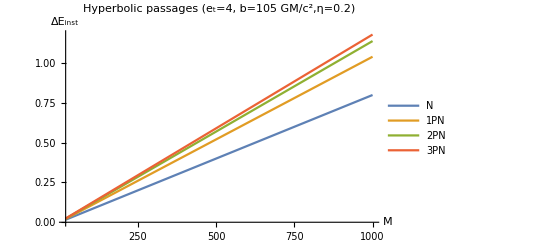

```mathematica
plot3=Plot[{EfluxN/.rel,Eflux1/.rel,Eflux2/.rel,Eflux/.rel},{M,20 ,1000 },PlotLegends->{"N","1PN","2PN","3PN"},PlotLabel->Style[Framed["Hyperbolic  passages (e_t=4, b=105 GM/c^2,η=0.2)"],8,Red,Background->Lighter[Cyan]],AxesLabel->{M,Subscript[ΔE, inst]}]
```

```mathematica
Export["m105e.jpg",plot3,ImageResolution->300]
```

m105e.jpg

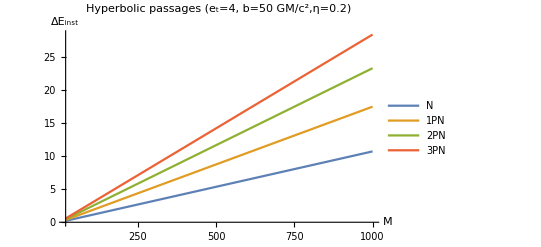

```mathematica
plot4=Plot[{EfluxN/.rel3,Eflux1/.rel3,Eflux2/.rel3,Eflux/.rel3},{M,20 ,1000 },PlotLegends->{"N","1PN","2PN","3PN"},PlotLabel->Style[Framed["Hyperbolic  passages (e_t=4, b=50 GM/c^2,η=0.2)"],8,Red,Background->Lighter[Cyan]],AxesLabel->{M,Subscript[ΔE, inst]}]
```

```mathematica
Export["m50e.jpg",plot4,ImageResolution->300]
```

m50e.jpg